```mathematica
allfk=Import["/Users/Tommy/Documents/UNC Charlotte/Research with Ogle/3 IA Fluorimeter and UVVis/fluorescence kinetics.csv"];

importfk[file_]:=
Module[{datacolumn,name,time,fluor,listname,templist,exwave,emwave,varname,min,max},
datacolumn=3;(*the desired data starts here*)
listname=ToExpression[StringJoin["list",ToString[Unevaluated[file]]]];
(*creates name of list of lists as list"inputfilename"*)
templist={};
(*makes templist an empty list to which names can be added*)
While[datacolumn≤Length[file[[1]]](*continues while datacolumn index is ≤ width of spectra*),
name=ToExpression[Evaluate[file[[6,datacolumn]]]];(*converts desired name from string to symbol*)
If[Head[name]===List,(*if name is already a list, skip it, increment datacolumn, and move on, if not, then do everything*)
++datacolumn;
++datacolumn,
templist=Insert[templist,ToString[name],-1];
(*adds name of current file to the list*)
time=file[[22;;-1,datacolumn-1]];
(*selects only data not header rows for the time values*)
fluor=file[[22;;-1,datacolumn]];(*these are the absorbance values for the current set of data*)
exwave=file[[3,datacolumn]];
emwave=file[[4,datacolumn]];
(*this are the wavelength used for the kinetics experiment*)
varname=file[[6,datacolumn]];
(*this stores the file name to make processing later easier*)
min=file[[17,datacolumn]];
(*the lowerbound for graphing*)
max=file[[16,datacolumn]];
time=DeleteCases[time,""];(*deletes blank items*)
fluor=DeleteCases[fluor,""];
Evaluate[name]={Evaluate[{time,fluor}ᵀ],max,min,varname,exwave,emwave};
(*saves data with name (which must be evaluated so they won't all be called "name") and is transposed so that they end up in columns correctly, followed by the wavelength and desired filename at the bottom*)
++datacolumn;
++datacolumn;]
(*increments column by 2 to get to the next set of data two columns over*)];
If[Head[listname]===List,
AppendTo[listname,templist],
Evaluate[listname]=templist[[1;;-2]]
(*sets listname to value of templist which is list of strings of the names of the lists created in the while loop.
Assumes extra blank entries all with the same name at the end*)]]
SetAttributes[importfk,HoldAllComplete]

exportPDFfk[name_]:=(*this takes a single argument that is a string of the name of the kinetics variable to be exported with name "kinname.pdf"*)Export[StringJoin[{name,".pdf"}](*name is the name of the file (already a string).pdf, which automatically sets the file format*),
makefkPlot[ToExpression[name]]]
(*SetAttributes[ExportPDFSpectrum,HoldFirst]*)

makefkPlot[kin_]:=Module[{data,ylabel,exwave,emwave,ticks,ticksmajor,ticksminor,ticksminorloc,min,max},
data=kin[[1]](*this range excludes wavelength and name listed at the end*);
min=kin[[-4]];(*lower bound for graph*)
max=kin[[-5]];
exwave=kin[[-2]];
emwave=kin[[-1]];
(*wavelengths used for this experiment for labeling*)
ylabel=StringJoin["ex: ",ToString[exwave]," nm, em: ",ToString[emwave]," nm\nfluorescence"];
(*defines label for y axis with ex and em wavelengths*)
ticks=FindDivisions[{data[[1,1]],data[[-1,1]]},6];
ticksmajor=FindDivisions[{data[[1,1]],data[[-1,1]]},6];
ticksminorloc=Complement[FindDivisions[{data[[1,1]],data[[-1,1]]},30],FindDivisions[{data[[1,1]],data[[-1,1]]},6]];
ticksminor={};
Do[AppendTo[ticksminor,Evaluate[Join[{ticksminorloc[[i]]},{"",{.006,0}}]]],{i,Length[ticksminorloc]}];
ticks=Join[ticksmajor,ticksminor];
(*manually defines x ticks because they weren't fitting with the enlarged font size*)
ListPlot[data,PlotStyle->Black,AxesOrigin->{data[[1,1]],0},Joined->True,Filling->Axis,FillingStyle->LightGray,PlotRange->{{data[[1,1]],data[[-1,1]]},{min,max}},Frame->True,FrameLabel->{{ylabel,""},{"time (s)",""}},LabelStyle->18,FrameTicks->{{Automatic,None},{ticks,None}},FrameStyle->16]]

exportfk[list_]:=Module[{index},
index=0;
While[index<Dimensions[list][[1]],
index++;
exportPDFfk[list[[index]]];
Print[index]]]

modelfks[list_]:=
Module[{index,model,name,templist,listname},
index=0;
templist={};
listname=
ToExpression[StringJoin[ToString[Unevaluated[list]],"wmodels"]];
While[index<Dimensions[list][[1]],
name=ToExpression[StringJoin[Evaluate[list[[++index]]],"wmodel"]];
AppendTo[templist,ToString[name]];
model=nonLinModFitmodel[ToExpression[list[[index]]][[1]]];
Evaluate[name]=Insert[ToExpression[list[[index]]],model,-6];];
Evaluate[listname]=templist]
SetAttributes[modelfks,HoldAllComplete]


nonLinModFitmodel[inputdata_]:=
Module[{maxtime,length},
length=Dimensions[inputdata][[1]];
maxtime=inputdata[[length,1]];
NonlinearModelFit[inputdata,a ⅇ^(-kH (t-t0))+b(1-ⅇ^(-kH (t-t0))),{{kH,.001},
{a,inputdata[[1,2]]},
{b,inputdata[[length,2]]}
(*these make the starting estimates for a and b the first and last values of the kinetics run*),t0},t]]

nonLinModFitmodelx[inputdata_]:=
Module[{maxtime,length,model,dataplot},
length=Dimensions[inputdata][[1]];
maxtime=inputdata[[length,1]];
dataplot=ListPlot[inputdata,PlotStyle->Red,ImageSize->{150,150},Ticks->{None,Automatic}]
(*graph to display in Input box to show the user what it looks like to help make good guesses. I don't know that this works*)
model=NonlinearModelFit[inputdata,a ⅇ^(-kH (t-t0))+b(1-ⅇ^(-kH (t-t0))),{{kH,.001},
{a,Input["starting 'a' estimate?"dataplot,inputdata[[1,2]]]},{b,Input["starting 'b' estimate?"dataplot,inputdata[[length,2]]]},t0},t]]

exportModelParameters[list_]:=
Module[{index,k,templist,listname},
index=0;
templist={};
listname=
ToExpression[StringJoin[ToString[Unevaluated[list]],"kHs"]];
While[index<Dimensions[list][[1]],
Print[list[[++index]]];
k=
kH /.ToExpression[list[[index]]][[-6]]["BestFitParameters"];
Print[k];
AppendTo[templist,{"",k}](*want empty unit here to fit with the data in the Excel document*)
];
Export[StringJoin[ToString[listname],".csv"],Row[Flatten[templist]]];(*Also want it as a row vector to fit with the data formatting in Excel*)
Evaluate[listname]=Flatten[templist]]
SetAttributes[exportModelParameters,HoldAllComplete]

printModelParameters[list_]:=
Module[{index,model,maxtime,length,data},
index=0;
While[index<Dimensions[list][[1]],
Print[list[[++index]]];
model=ToExpression[list[[index]]][[-6]];
data=ToExpression[list[[index]]][[1]];
length=Dimensions[data][[1]];
maxtime=data[[length,1]];
Print[Show[
Plot[model[t],{t,0,maxtime}],
ListLinePlot[data,PlotStyle->Thick]
]];
Print[model["BestFitParameters"]];
]
]
```

```mathematica
Quit[]
```

```mathematica
importfk[allfk]
exportfk[listallfk]
modelfks[listallfk]
exportModelParameters[listallfkwmodels]
printModelParameters[listallfkwmodels]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{0, 25, 50, 75, 100, 125, 150, 175, 200, 225, 250, 275, 300, 325, 350, 375, 400, 425, 450, 475, 500, 525, 550, 575, 600, 625, 650, 675, 700, 725, 750, 775, 800, 825, 850, 875, 900, 925, 950, 975, 1000, 1025, 1050, 1075, 1100, 1125, 1150, 1175, 1200, 1225, « 59 »}, {}} cannot be transposed.

{fkbsap380,fkbsap415,fkbufferp380,fkbufferp415,fkwaterp380,fkwaterp415,fk2bufferpw380,fk3insulinpw380,fk3bsapw380,fk3waterpd380,fk3bufferpd380,fk3insulinpd380,fk3bsapd380,fk3waternd380,fk3waterpw415,fk2bufferpw415,fk3insulinpw415,fk3bsapw415,fk3waterpd415,fk3bufferpd415,fk3insulinpd415,fk3bsapd415,fk3waternd415,fk3buffernd415,fk3insulinnd415,fk3bsand415,fk3waterpwlater380,fk3waterpwlater415,fk3waterpdlater380,fk3waterpdlater415,fk3waterndlater380,fk3waterndlater415}

fkbsap380wmodel

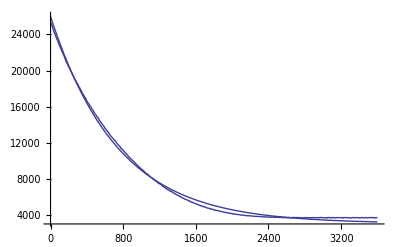

{kH→0.00135942,a→34387.7,b→3054.95,t0→-229.479}

fkbsap415wmodel

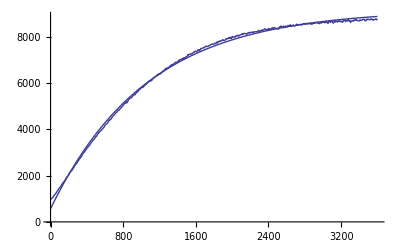

{kH→0.000946098,a→-125.521,b→9176.32,t0→-81.7923}

fkbufferp380wmodel

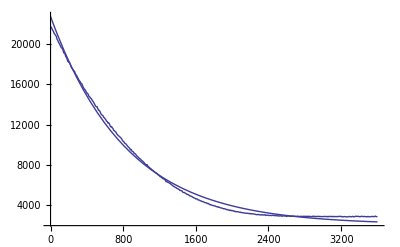

{kH→0.00120271,a→22770.1,b→2097.05,t0→-3.39693}

fkbufferp415wmodel

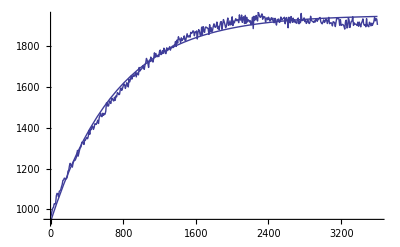

{kH→0.00138182,a→912.701,b→1954.46,t0→-17.5553}

fkwaterp380wmodel

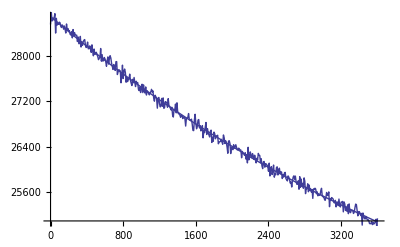

{kH→0.00017703,a→28206.7,b→21038.7,t0→367.303}

fkwaterp415wmodel

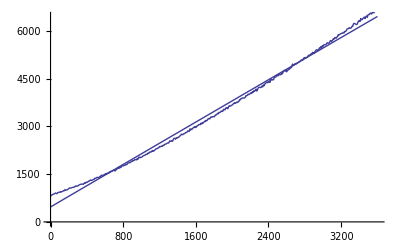

{kH→2.85866×10^-6,a→526.512,b→584896.,t0→34.4664}

fk2bufferpw380wmodel

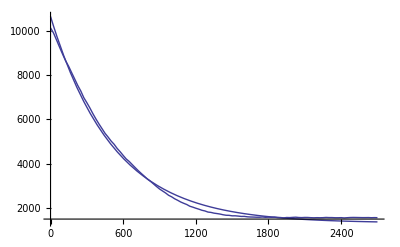

{kH→0.00193367,a→7179.45,b→1322.1,t0→240.389}

fk3insulinpw380wmodel

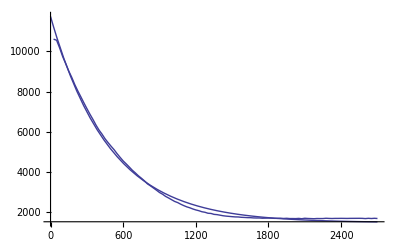

{kH→0.00207102,a→14434.3,b→1454.96,t0→-112.113}

fk3bsapw380wmodel

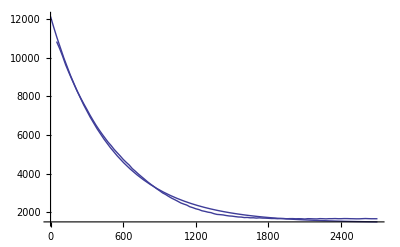

{kH→0.0020453,a→6128.28,b→1457.03,t0→403.951}

fk3waterpd380wmodel

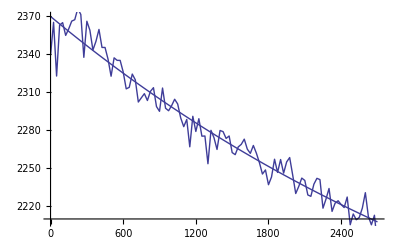

{kH→0.00021963,a→2367.65,b→2008.07,t0→20.3472}

fk3bufferpd380wmodel

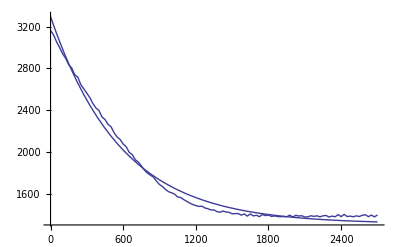

{kH→0.00172229,a→4800.59,b→1310.32,t0→-326.707}

fk3insulinpd380wmodel

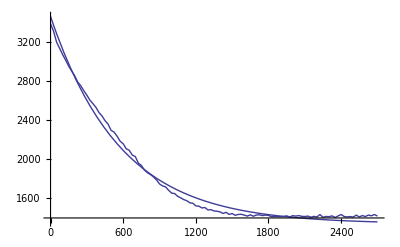

{kH→0.00173058,a→2896.46,b→1339.87,t0→178.342}

fk3bsapd380wmodel

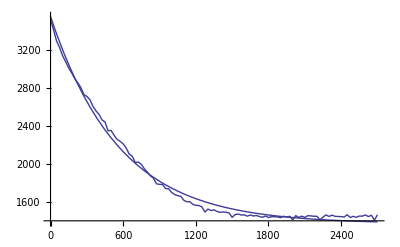

{kH→0.00176266,a→8109.83,b→1369.94,t0→-640.945}

fk3waternd380wmodel

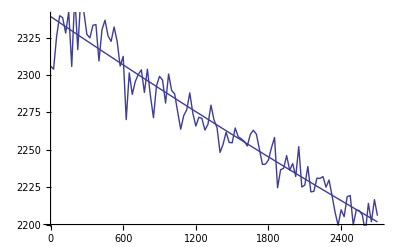

{kH→0.0000569625,a→2321.57,b→1374.78,t0→324.813}

fk3waterpw415wmodel

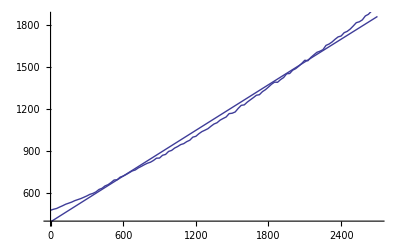

{kH→3.56882×10^-6,a→409.909,b→152973.,t0→28.2849}

fk2bufferpw415wmodel

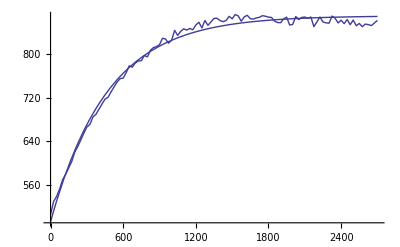

{kH→0.00213043,a→511.322,b→870.174,t0→25.0401}

fk3insulinpw415wmodel

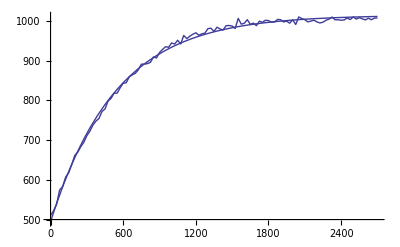

{kH→0.00186296,a→440.668,b→1014.41,t0→-52.4868}

fk3bsapw415wmodel

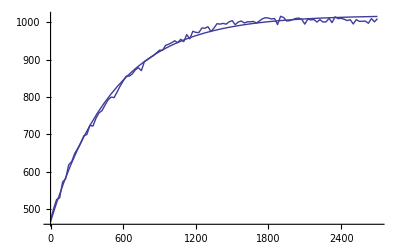

{kH→0.00193275,a→-684.02,b→1018.31,t0→-582.752}

fk3waterpd415wmodel

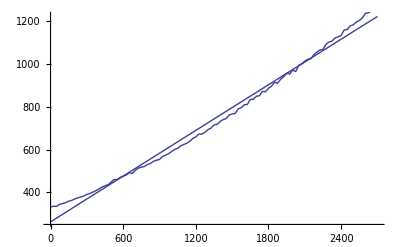

{kH→3.054×10^-6,a→276.735,b→117168.,t0→41.5914}

fk3bufferpd415wmodel

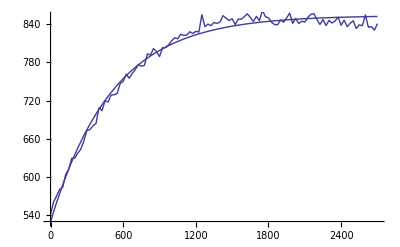

{kH→0.00197304,a→479.559,b→853.841,t0→-72.4446}

fk3insulinpd415wmodel

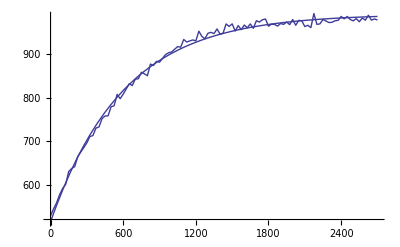

{kH→0.00166814,a→453.501,b→991.819,t0→-72.1272}

fk3bsapd415wmodel

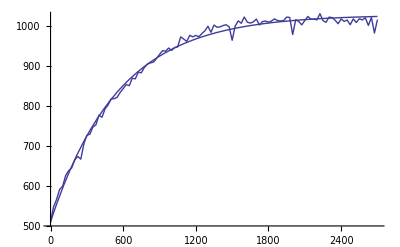

{kH→0.00179122,a→641.236,b→1027.6,t0→163.124}

fk3waternd415wmodel

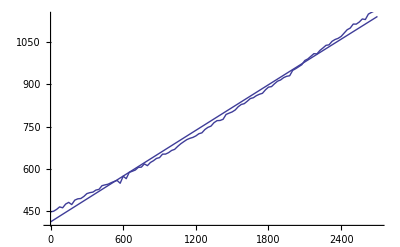

{kH→3.57349×10^-6,a→418.523,b→76280.6,t0→22.422}

fk3buffernd415wmodel

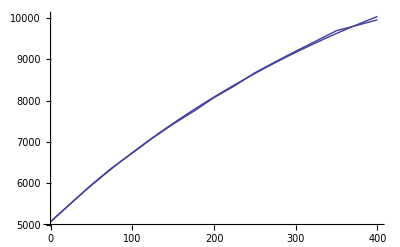

{kH→0.00218687,a→5438.44,b→13589.6,t0→20.5847}

fk3insulinnd415wmodel

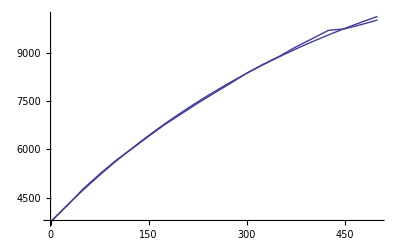

{kH→0.0021791,a→2334.8,b→13341.9,t0→-63.4478}

fk3bsand415wmodel

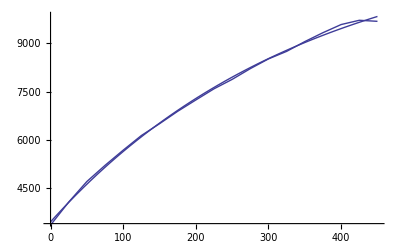

{kH→0.00283879,a→-655.909,b→12297.2,t0→-134.423}

fk3waterpwlater380wmodel

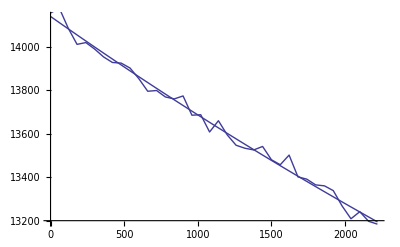

{kH→0.000104047,a→14245.7,b→9559.2,t0→-221.448}

fk3waterpwlater415wmodel

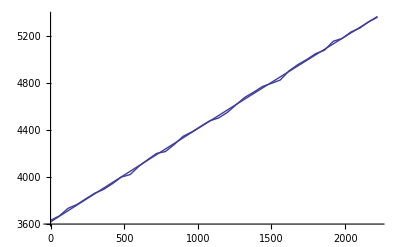

{kH→0.0000135506,a→3611.02,b→62718.7,t0→-9.30234}

fk3waterpdlater380wmodel

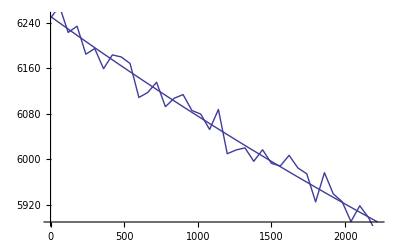

{kH→0.000125135,a→6211.,b→4762.12,t0→219.888}

fk3waterpdlater415wmodel

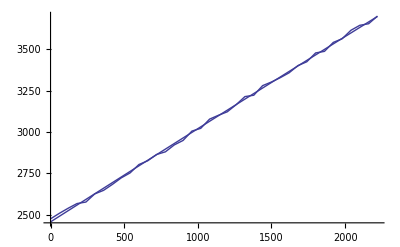

{kH→0.0000116705,a→2453.52,b→51099.2,t0→-3.77611}

fk3waterndlater380wmodel

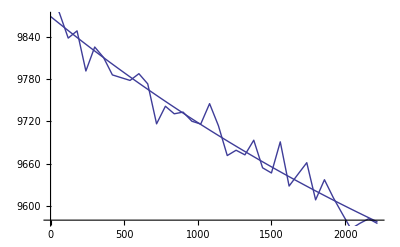

{kH→0.000239913,a→9906.14,b→9162.96,t0→-213.183}

fk3waterndlater415wmodel

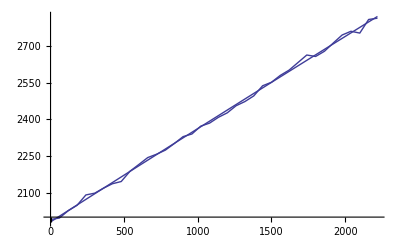

{kH→0.0000138255,a→1978.31,b→29816.7,t0→-5.33953}

```mathematica
printModelParameters[listallfkwmodels]
```